

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Solve[√a==b,a,Reals]
```

{{a→ConditionalExpression[b^2,b>0]}}

```mathematica
Map[ArcCurvature[{x,#},x],{x x, x x x}]
```

{0[x^2],0[x^3]}

```mathematica
Map[ArcCurvature[{x,#},x]&,{x x, x x x}]
```

{2/((1+4 x^2)^(3/2)),(6 Abs[x])/((1+9 x^4)^(3/2))}

```mathematica
FullSimplify[Map[ArcCurvature[{x,#},x]&,{x x, x x x}],x∈Reals]
```

{2/((1+4 x^2)^(3/2)),(6 Abs[x])/((1+9 x^4)^(3/2))}

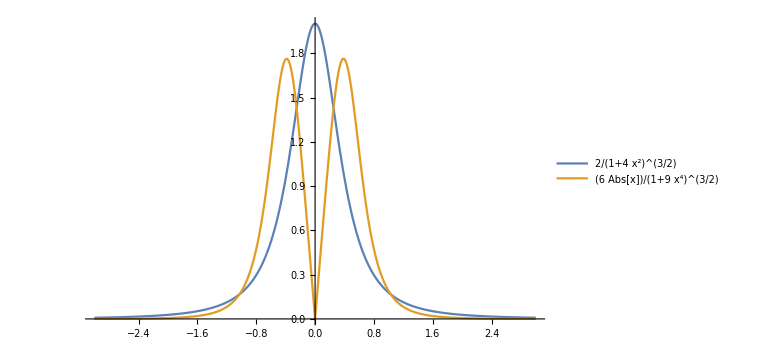

```mathematica
Plot[
{2/((1+4 x^2)^(3/2)),(6 Abs[x])/((1+9 x^4)^(3/2))}
,{x,-3,3},PlotLegends->"Expressions",PlotRange->Full,ImageSize->Large]
```

```mathematica
NIntegrate[{2/((1+4 x^2)^(3/2)),(6 Abs[x])/((1+9 x^4)^(3/2))},{x,-10,10}]
```

{1.9975,1.99999}

```mathematica
FullSimplify[ArcCurvature[{x,α x},x],{x,α}∈Reals]
```

0

```mathematica
FullSimplify[ArcCurvature[{x,α x^a},x],{x,a,α}∈Reals]
```

√(x^(2+2 a)/((x^2+a^2 x^(2 a) α^2)^3)) Abs[(-1+a) a α]

```mathematica
FullSimplify[ArcCurvature[{x,x^a},x],{x,a}∈Reals]
```

√(x^(2+2 a)/((x^2+a^2 x^(2 a))^3)) Abs[-1+a] Abs[a]

```mathematica
FullSimplify[ArcCurvature[{x,x^a},x],x∈Reals∧a∈]
```

((-1+a) a Abs[x]^(1+a))/((x^2+a^2 x^(2 a))^(3/2))

```mathematica
Manipulate[
Plot[
{x^a,((-1+a) a Abs[x]^(1+a))/((x^2+a^2 x^(2 a))^(3/2))}
,{x,-5,5},PlotLegends->"Expressions",PlotRange->Full,ImageSize->Full]
,{a,0,20,1}
]
```

```mathematica
Manipulate[
Plot[
{x^a,((-1+a) a Abs[x]^(1+a))/((x^2+a^2 x^(2 a))^(3/2))}
,{x,-5,5},PlotLegends->"Expressions",PlotRange->Full,ImageSize->Large]
,{a,0,20,1}
]
```

```mathematica
Manipulate[
Plot[
{x^a,((-1+a) a Abs[x]^(1+a))/((x^2+a^2 x^(2 a))^(3/2))}
,{x,-5,5},PlotLegends->"Expressions",PlotRange->{{-5,5},{-5,5}},ImageSize->Large]
,{a,0,20,1}
]
```

```mathematica
ArcCurvature[{x,x^4},x]
```

(12 Abs[x]^2)/((1+16 x^6)^(3/2))

```mathematica
ArcCurvature[{x,x^3},x]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

```mathematica
(12 Abs[x]^2)/((1+16 x^6)^(3/2))-(6 Abs[x])/((1+9 x^4)^(3/2))
```

-(6 Abs[x])/((1+9 x^4)^(3/2))+(12 Abs[x]^2)/((1+16 x^6)^(3/2))

```mathematica
FullSimplify[-(6 Abs[x])/((1+9 x^4)^(3/2))+(12 Abs[x]^2)/((1+16 x^6)^(3/2))]
```

6 Abs[x] (-1/((1+9 x^4)^(3/2))+(2 Abs[x])/((1+16 x^6)^(3/2)))

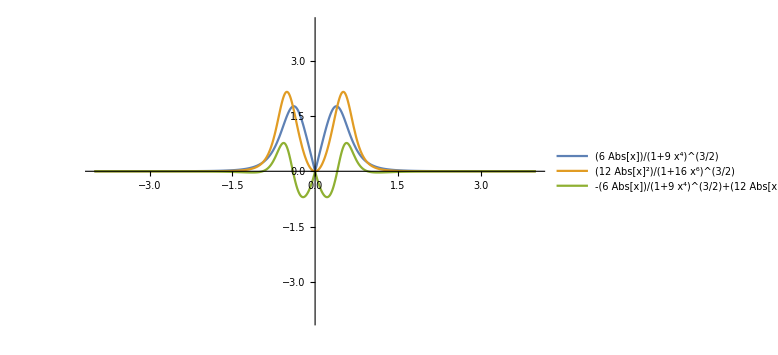

```mathematica
Plot[
{
(6 Abs[x])/((1+9 x^4)^(3/2)),
(12 Abs[x]^2)/((1+16 x^6)^(3/2)),
-(6 Abs[x])/((1+9 x^4)^(3/2))+(12 Abs[x]^2)/((1+16 x^6)^(3/2))

},{x,-4,4},PlotRange->{{-4,4},{-4,4}},PlotLegends->"Expressions",ImageSize->Large]
```

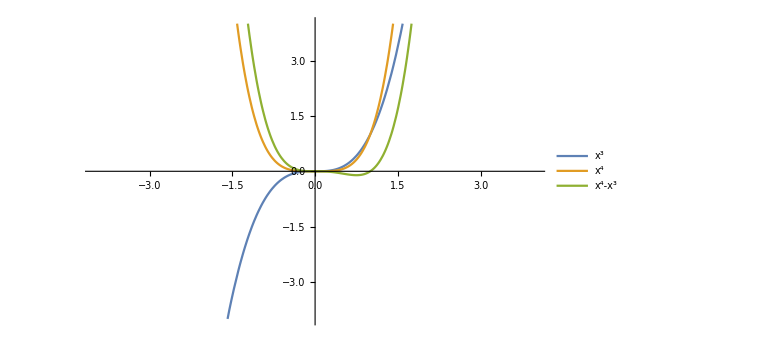
{-Graphics-,-Graphics-}

```mathematica
{
Plot[
{
(6 Abs[x])/((1+9 x^4)^(3/2)),
(12 Abs[x]^2)/((1+16 x^6)^(3/2)),
-(6 Abs[x])/((1+9 x^4)^(3/2))+(12 Abs[x]^2)/((1+16 x^6)^(3/2))

},{x,-4,4},PlotRange->{{-4,4},{-4,4}},PlotLegends->"Expressions",ImageSize->Large],
Plot[
{
x^3,
x^4,
x^4-x^3
},{x,-4,4},PlotRange->{{-4,4},{-4,4}},PlotLegends->"Expressions",ImageSize->Large]
}
```

```mathematica
ArcCurvature[{x,f[x]+g[x]},x]
```

√((f''[x]+g''[x])^2/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^3))

```mathematica
PowerExpand[√((f''[x]+g''[x])^2/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^3))]
```

(f''[x]+g''[x])/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^(3/2))

```mathematica
Expand[(f''[x]+g''[x])/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^(3/2))]
```

f''[x]/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^(3/2))+g''[x]/((1+f'[x]^2+2 f'[x] g'[x]+g'[x]^2)^(3/2))

```mathematica
ArcCurvature[{x,x^4-x^3},x]
```

(6 Abs[x] Abs[-1+2 x])/((1+9 x^4-24 x^5+16 x^6)^(3/2))

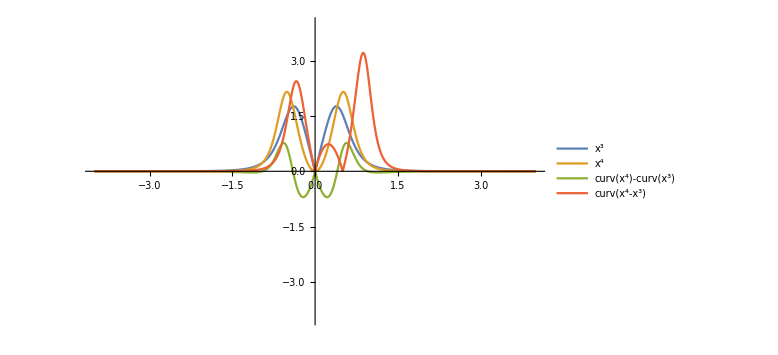

```mathematica
Plot[
{
(6 Abs[x])/((1+9 x^4)^(3/2)),
(12 Abs[x]^2)/((1+16 x^6)^(3/2)),
-(6 Abs[x])/((1+9 x^4)^(3/2))+(12 Abs[x]^2)/((1+16 x^6)^(3/2)),
(6 Abs[x] Abs[-1+2 x])/((1+9 x^4-24 x^5+16 x^6)^(3/2))

},{x,-4,4},PlotRange->{{-4,4},{-4,4}},PlotLegends->{x^3,x^4,curv[x^4]-curv[x^3],curv[x^4-x^3]},ImageSize->Large]
```

```mathematica
Plot[
{
x^3,
x^4,
x^4-x^3
},{x,-4,4},PlotRange->{{-4,4},{-4,4}},PlotLegends->"Expressions",ImageSize->Large]
```

-Graphics-

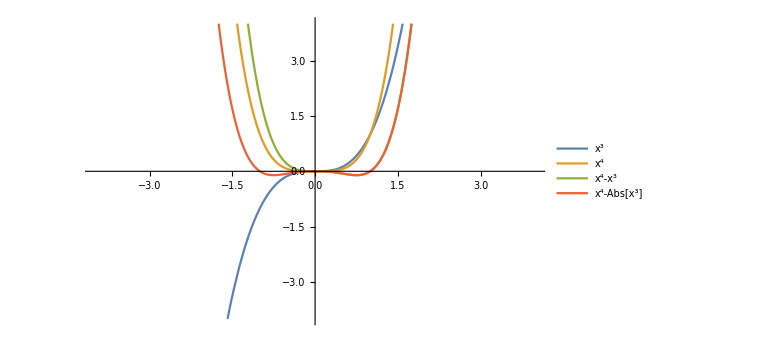

```mathematica
Plot[
{
x^3,
x^4,
x^4-x^3,
x^4-Abs[x^3]
},{x,-4,4},PlotRange->{{-4,4},{-4,4}},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
CountryData["IvoryCoast","Population"]
```

24294750 people

```mathematica
CountryData["Ghana","Population"]
```

28833629 people

```mathematica
CountryData["IvoryCoast","GDP"]
```

3.63726×10^10 $

```mathematica
CountryData["Ghana","GDP"]
```

4.26898×10^10 $

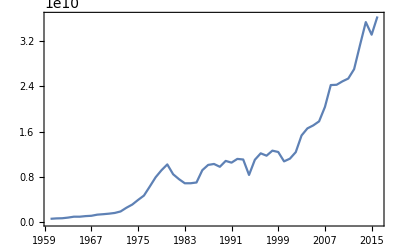

```mathematica
DateListPlot@CountryData["IvoryCoast",{"GDP",All}]
```

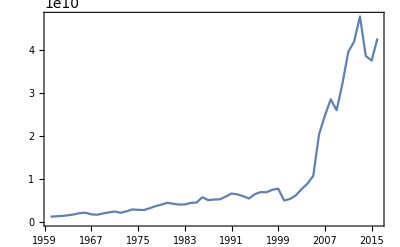

```mathematica
DateListPlot@CountryData["Ghana",{"GDP",All}]
```

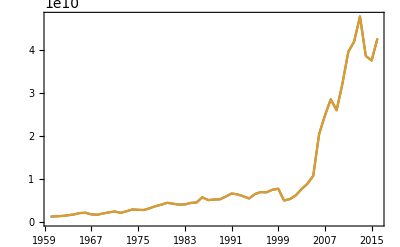

```mathematica
DateListPlot[{CountryData["Ghana",{"GDP",All}],CountryData["Ghana",{"GDP",All}]}]
```

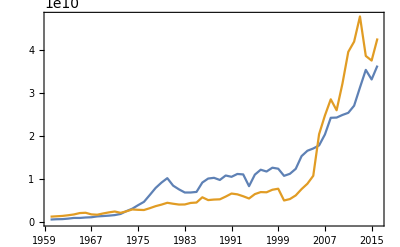

```mathematica
DateListPlot[{CountryData["IvoryCoast",{"GDP",All}],CountryData["Ghana",{"GDP",All}]}]
```

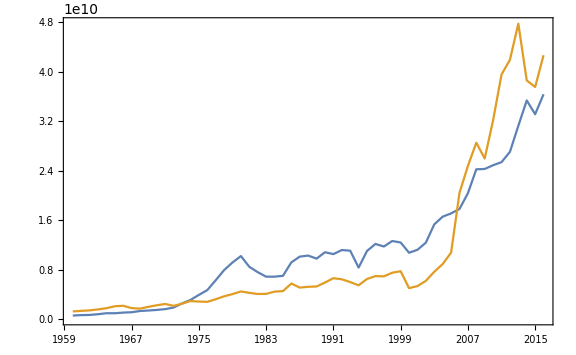

```mathematica
DateListPlot[{CountryData["IvoryCoast",{"GDP",All}],CountryData["Ghana",{"GDP",All}]},ImageSize->Large,PlotLegends->"Expressions"]
```

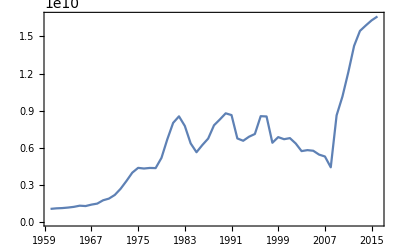

```mathematica
DateListPlot@CountryData["Zimbabwe",{"GDP",All}]
```

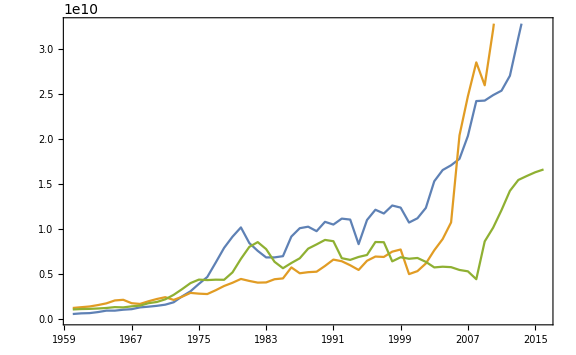

```mathematica
DateListPlot[{
CountryData["IvoryCoast",{"GDP",All}],
CountryData["Ghana",{"GDP",All}],
CountryData["Zimbabwe",{"GDP",All}]
},ImageSize->Large,PlotLegends->"Expressions"]
```

```mathematica
CountryData["Zimbabwe","Population"]
```

16529903 people

```mathematica
CountryData["Zimbabwe","GDP"]
```

1.662×10^10 $

```mathematica
CountryData["Zimbabwe","GDPPerCapita"]
```

1008.6 $

```mathematica
CountryData["Ghana","GDPPerCapita"]
```

1513.46 $

```mathematica
CountryData["IvoryCoast","GDPPerCapita"]
```

1526.2 $

```mathematica
Map[{#,CountryData[#,"GDPPerCapita"]}&,CountryData["Africa"]]
```

{{Algeria,3843.75 $},{Angola,3110.81 $},{Benin,789.44 $},{Botswana,6788.04 $},{Burkina Faso,649.73 $},{Burundi,285.727 $},{Cameroon,1032.65 $},{Cape Verde,2997.75 $},{Central African Republic,382.213 $},{Chad,664.296 $},{Comoros,775.08 $},{Democratic Republic of the Congo,444.505 $},{Djibouti,1862.17 $},{Egypt,3514.49 $},{Equatorial Guinea,8333.24 $},{Eritrea,544.462 $},{Ethiopia,706.758 $},{Gabon,7179.34 $},{Gambia,473.19 $},{Ghana,1513.46 $},{Guinea,508.145 $},{Guinea-Bissau,620.215 $},{Ivory Coast,1526.2 $},{Kenya,1455.36 $},{Lesotho,998.134 $},{Liberia,455.371 $},{Libya,4643.31 $},{Madagascar,401.319 $},{Malawi,300.795 $},{Mali,780.507 $},{Mauritania,1077.56 $},{Mauritius,9627.6 $},{Mayotte,4900. $},{Morocco,2832.43 $},{Mozambique,382.069 $},{Namibia,4140.46 $},{Niger,363.227 $},{Nigeria,2177.99 $},{Republic of the Congo,1528.24 $},{Réunion,14390. $},{Rwanda,702.836 $},{Saint Helena, Ascension and Tristan da Cunha,2500. $},{São Tomé and Príncipe,1756.06 $},{Senegal,958.074 $},{Seychelles,15075.7 $},{Sierra Leone,496.049 $},{Somalia,434.209 $},{South Africa,5273.59 $},{South Sudan,758.721 $},{Sudan,2415.04 $},{Eswatini,2775.15 $},{Tanzania,879.194 $},{Togo,578.462 $},{Tunisia,3688.65 $},{Uganda,615.309 $},{Western Sahara,2500. $},{Zambia,1178.39 $},{Zimbabwe,1008.6 $}}

```mathematica
Grid@ReverseSortBy[Map[{#,CountryData[#,"GDPPerCapita"]}&,CountryData["Africa"]],Last]
```

Seychelles | 15075.7 $
Réunion | 14390. $
Mauritius | 9627.6 $
Equatorial Guinea | 8333.24 $
Gabon | 7179.34 $
Botswana | 6788.04 $
South Africa | 5273.59 $
Mayotte | 4900. $
Libya | 4643.31 $
Namibia | 4140.46 $
Algeria | 3843.75 $
Tunisia | 3688.65 $
Egypt | 3514.49 $
Angola | 3110.81 $
Cape Verde | 2997.75 $
Morocco | 2832.43 $
Eswatini | 2775.15 $
Western Sahara | 2500. $
Saint Helena, Ascension and Tristan da Cunha | 2500. $
Sudan | 2415.04 $
Nigeria | 2177.99 $
Djibouti | 1862.17 $
São Tomé and Príncipe | 1756.06 $
Republic of the Congo | 1528.24 $
Ivory Coast | 1526.2 $
Ghana | 1513.46 $
Kenya | 1455.36 $
Zambia | 1178.39 $
Mauritania | 1077.56 $
Cameroon | 1032.65 $
Zimbabwe | 1008.6 $
Lesotho | 998.134 $
Senegal | 958.074 $
Tanzania | 879.194 $
Benin | 789.44 $
Mali | 780.507 $
Comoros | 775.08 $
South Sudan | 758.721 $
Ethiopia | 706.758 $
Rwanda | 702.836 $
Chad | 664.296 $
Burkina Faso | 649.73 $
Guinea-Bissau | 620.215 $
Uganda | 615.309 $
Togo | 578.462 $
Eritrea | 544.462 $
Guinea | 508.145 $
Sierra Leone | 496.049 $
Gambia | 473.19 $
Liberia | 455.371 $
Democratic Republic of the Congo | 444.505 $
Somalia | 434.209 $
Madagascar | 401.319 $
Central African Republic | 382.213 $
Mozambique | 382.069 $
Niger | 363.227 $
Malawi | 300.795 $
Burundi | 285.727 $

```mathematica
Grid@TakeLargestBy[Map[{#,CountryData[#,"GDPPerCapita"]}&,CountryData[]],Last,10]
```

Liechtenstein | 168146. $
Monaco | 163352. $
Luxembourg | 102831. $
Bermuda | 85748.1 $
Isle of Man | 81672. $
Switzerland | 78812.7 $
Macau | 73187. $
Norway | 70812.5 $
Cayman Islands | 64104.8 $
Ireland | 61606.5 $

```mathematica
CountryData[{"Liechtenstein","Luxembourg"},"Population"]
```

CountryData::notent: {"Liechtenstein", "Luxembourg"} is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData[{Liechtenstein,Luxembourg},Population]

```mathematica
CountryData["Luxembourg","Population"]
```

583455 people

```mathematica
CountryData["Liechtenstein","Population"]
```

37922 people

```mathematica
CountryData["Monaco","Population"]
```

38695 people

```mathematica
Grid@TakeLargestBy[Map[{#,CountryData[#,"GDPPerCapita"]}&,CountryData[]],Last,30]
```

Liechtenstein | 168146. $
Monaco | 163352. $
Luxembourg | 102831. $
Bermuda | 85748.1 $
Isle of Man | 81672. $
Switzerland | 78812.7 $
Macau | 73187. $
Norway | 70812.5 $
Cayman Islands | 64104.8 $
Ireland | 61606.5 $
Iceland | 59976.9 $
Qatar | 59330.9 $
United States | 57466.8 $
Jersey | 57000. $
Faroe Islands | 54117.8 $
Denmark | 53417.7 $
British Virgin Islands | 53302.5 $
Singapore | 52960.7 $
Sweden | 51599.9 $
Australia | 49927.8 $
San Marino | 47908.6 $
Netherlands | 45294.8 $
Guernsey | 44600. $
Austria | 44176.5 $
Hong Kong | 43681.1 $
Finland | 43090.2 $
Canada | 42157.9 $
Germany | 41936.1 $
Belgium | 41096.2 $
United Kingdom | 39899.4 $

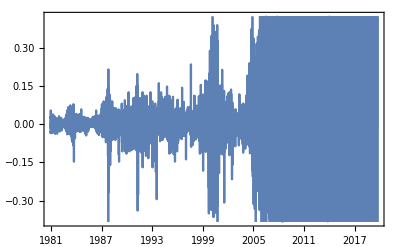

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot@Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
]]
```

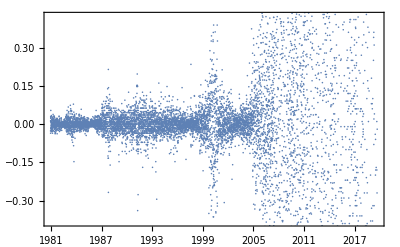

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Joined->False,ImageSize->Full,ColorFunction->"DarkRainbow"]
]]
```

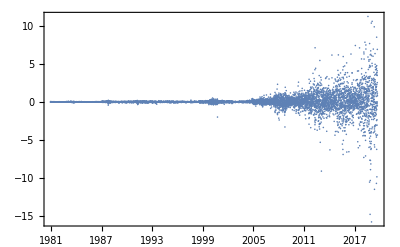

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}]
,Joined->False,ImageSize->Full,ColorFunction->"DarkRainbow",PlotRange->Full]
]]
```

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
LinearModelFit[ts["Values"],x,x]
]]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[QuantityArray[…],x,x]

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
First@ts["Dates"]
]]
```

Fri 12 Dec 1980 00:00:00GMT-7.

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
LinearModelFit[Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],x,x]
]]]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

DateListPlot::ldata: LinearModelFit[{{DateObject[{1980,12,12,0,0,0.},Instant,Gregorian,-7.],-0.03},{DateObject[{1980,12,15,0,0,0.},Instant,Gregorian,-7.],-0.04},{DateObject[{1980,12,16,0,0,0.},Instant,Gregorian,-7.],0.01},«45»,{DateObject[{1981,2,23,0,0,0.},Instant,Gregorian,-7.],-0.02},{DateObject[{1981,2,24,0,0,0.},Instant,Gregorian,-7.],0.03},«9730»},x,x] is not a valid dataset or list of datasets.

DateListPlot[LinearModelFit[{{Fri 12 Dec 1980 00:00:00GMT-7.,-0.03 $},{Mon 15 Dec 1980 00:00:00GMT-7.,-0.04 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.01 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.01 $},9772,{Wed 11 Sep 2019 00:00:00GMT-7.,-0.50 $},{Thu 12 Sep 2019 00:00:00GMT-7.,-4.34 $},{Fri 13 Sep 2019 00:00:00GMT-7.,1.15 $},{Mon 16 Sep 2019 00:00:00GMT-7.,0.80 $}},x,x]]
 |  |  |  |

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
LinearModelFit[Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],x,x]
]]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{Fri 12 Dec 1980 00:00:00GMT-7.,-0.03 $},{Mon 15 Dec 1980 00:00:00GMT-7.,-0.04 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.01 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.01 $},9772,{Wed 11 Sep 2019 00:00:00GMT-7.,-0.50 $},{Thu 12 Sep 2019 00:00:00GMT-7.,-4.34 $},{Fri 13 Sep 2019 00:00:00GMT-7.,1.15 $},{Mon 16 Sep 2019 00:00:00GMT-7.,0.80 $}},x,x]
 |  |  |  |

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Differences@ts["Values"]},
LinearModelFit[
Transpose[{
Range@Length@values,
values
}],x,x]
]]]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{1,-0.03 $},{2,-0.04 $},{3,0.01 $},{4,0.01 $},{5,0.03 $},{6,0.02 $},{7,0.02 $},{8,0.03 $},{9,0.05 $},{10,0.01 $},{11,-0.02 $},{12,-0.02 $},{13,0.01 $},{14,-0.01 $},{15,-0.03 $},{16,-0.02 $},{17,-0.01 $},{18,0.03 $},{19,-0.00 $},{20,-0.02 $},{21,0.00 $},{22,0.01 $},{23,-0.00 $},{24,0.03 $},9732,{9757,-6.22 $},{9758,-1.01 $},{9759,4.76 $},{9760,3.85 $},{9761,0.01 $},{9762,2.28 $},{9763,-0.18 $},{9764,-9.82 $},{9765,3.85 $},{9766,-2.33 $},{9767,1.37 $},{9768,3.48 $},{9769,-0.27 $},{9770,-3.04 $},{9771,3.49 $},{9772,4.09 $},{9773,-0.02 $},{9774,0.91 $},{9775,2.53 $},{9776,6.89 $},{9777,-0.50 $},{9778,-4.34 $},{9779,1.15 $},{9780,0.80 $}},x,x]
 |  |  |  |

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Map[QuantityMagnitude,ts["Values"]]},
LinearModelFit[
Transpose[{
Range@Length@values,
values
}],x,x]
]]]
```

FittedModel[-37.2971+0.01361 x]

```mathematica
%62["Function"]
```

-37.2971+0.01361 #1&

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Map[QuantityMagnitude,ts["Values"]]},
LinearModelFit[
Transpose[{
Range@Length@values,
values
}],x,x]
]]]
```

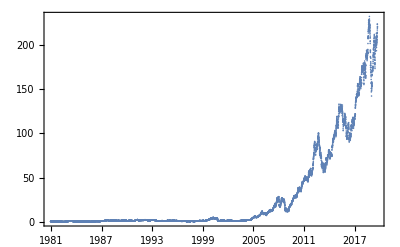

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Map[QuantityMagnitude,ts["Values"]]},
DateListPlot[
Transpose[{
ts["Dates"],
values
}]
,Joined->False,ImageSize->Full,ColorFunction->"DarkRainbow",PlotRange->Full]
]]]
```

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Map[QuantityMagnitude,ts["Values"]]},
DateListLogPlot[
Transpose[{
ts["Dates"],
values
}]
,Joined->False,ImageSize->Full,ColorFunction->"DarkRainbow",PlotRange->Full]
]]]
```

-Graphics-

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Differences@ts["Values"]},
DateListLogPlot[
Transpose[{
ts["Dates"][[;;-2]],
values
}]
,Joined->False,ImageSize->Full,ColorFunction->"DarkRainbow",PlotRange->Full]
]]]
```

-Graphics-

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
With[{values=Differences@ts["Values"]},
DateListPlot[
Transpose[{
ts["Dates"][[;;-2]],
values
}]
,Joined->False,ImageSize->Full,ColorFunction->"DarkRainbow",PlotRange->Full]
]]]
```

-Graphics-